# Four point spectrum

#### Initialize notebook (automatic).

```mathematica
SetDirectory[NotebookDirectory[]];
<<FourPointSpectrum`
```

### Manipulate based on β and accuracy ϵ=10^(-n).

Show the whole set (collection of intervals).

```mathematica
Manipulate[image[β, 10^(-n)],{{β,0.5},0.01,0.9,0.002}, {{n,4}, 1,8}]
```

Show the endpoints of the intervals for the current β value.

```mathematica
Manipulate[points[β, 10^(-n)],{{β,0.5},0.01,0.9,0.002}, {{n,4}, 1,8}]
```

### Exact computations (β must be exact).

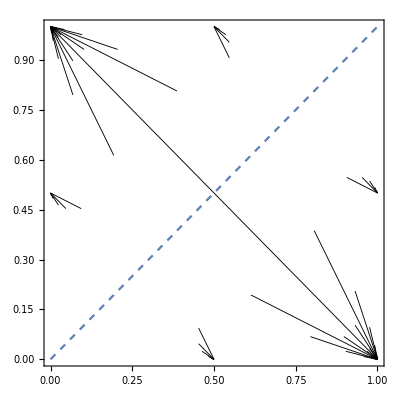
-Graphics-1/(2 √2)

-2/7 (-3+√2)

{{1/14 (-5+4 √2),-2/7 (-3+√2)},{1/7 (-5+4 √2),-2/7 (-3+√2)}}

```mathematica
β=Sqrt[2]/4;
image[β]
(* only upper half *)
ints=intervals[β][[All,2]]//Select[#,#[[1]]<=#[[2]]&]&;
(* minimal y *)
miny = Min[ints[[All,2]]]//FullSimplify
(* all points with minimal y *)
Select[ints,#[[2]]==miny&]//SortBy[#,First]&//FullSimplify
```

### Testing memory and speed limits.

A short time with 8 GB of rational numbers, 5 minutes:

```mathematica
intervals[98/100]//AbsoluteTiming//First
```

305.40418

A short time with 5 GB of memory used, 8 seconds:

```mathematica
intervals[0.98, 10^-8]//AbsoluteTiming;
{%[[1]],%[[2]]//Length}
```

{7.92717,38579858}

A short time with 20 GB of memory used, 1 minute:

```mathematica
intervals[0.99]//AbsoluteTiming;
{%[[1]],%[[2]]//Length}
```

{57.82738,143419042}

### Save an image.

```mathematica
im = image[0.95] // AbsoluteTiming;
%[[1]]
Export["~/image.eps", im[[2, 1]]]
```

0.19386

image.pdf

### Save a movie.

Exporting takes much longer than generating the data.

```mathematica
B=0.9;
db=0.002;
animate=Monitor[Table[image[N[b]],{b,db,B,db}],Row[{ProgressIndicator[b,{db,B}],"b=",N[b]}]]//AbsoluteTiming;
animate[[1]]
Export["~/movie.avi",animate[[2,All,1]],ImageSize->800]
```

0.9

0.002

0.51211

~/movie.avi